# Probability and Probability Distribution

A probability distribution of a random variable tells us the probabilities of all the possible outcomes (for discrete random variables) of the variable or ranges of values (for continuous random variables). A probability distribution shows us the regular, predictable distribution of outcomes in a large number of repetitions of a random variable.

## Probability Rules

The probability of an event (e.g. a randomly chosen person has blood type A) can be estimated by the relative frequency with which the event occurs in a long series of trials.

Example: All human blood can be typed as O, A, B or AB. According to Stanford University’s Blood Center, these are the probabilities of human blood types in the United States

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Georgia",FontSize->16}];
PieChart[{.44,.42,.1,.04},ChartLabels->{"O 44%","A 42%", "B 10%", "AB 4%"},ChartElementFunction->"GlassSector",ChartStyle->"Pastel",PlotLabel->"Blood Types"]
```

-Graphics-

The probability distribution of blood type above has the following characteristics:

Each outcome has a probability.

Each probability is between 0 and 1.

The sum of all the probabilities is 1.

### Discussions

It is unlikely that a person has blood type AB. Imagine that you (or the doctor) see a person has blood type AB. Is it more likely, less likely, or equally likely that the next person you see has blood type AB? Give a reason for your answer.

The blood type which occurs most often is O. Suppose you see three persons with blood type O  in a row. Is it more likely, less likely, or equally likely that the next person you see has blood type O?

Will the blood type of a random person impact the blood type of ? Why or why not?

Suppose we wanted to determine the probability of two randomly chosen person with blood type O. To answer this question, we must understand the concept of independent events. An event is a collection of one or more outcomes in a probability distribution. We can use probability rules to find the probability that multiple events will occur.

### The Multiplication Rule (Independent Events)

If two events are independent, when one event occurs, it does not change the probability that the other event will occur. It is neither more likely or less likely that the second event will occur. The probability that two independent events occur is the product of the individual probabilities.

P(A and B) = P(A)·P(B)

This rule of multiplication can be extended to three or more independent events.

### Examples

What is the probability that two randomly chosen persons both have blood type O?

What is the probability that three randomly chosen persons all have blood type O?

What is more likely to occur: two randomly chosen persons both have blood type O, or two randomly chosen persons both have blood type A?

Suppose we wanted to determine the probability that a randomly chosen person does NOT have blood type O.  To answer this question, we must understand the concept of complement events. The complement of an event contains all of the outcomes in a probability distribution that are not in the event.

### The Complement Rule

The sum of the probability of an event and the probability of the event’s complement is 1.

P(A) +P(not A)=1

```mathematica
PieChart[{.44,.56},ChartLabels->{"O 44%","not O 56%"},ChartElementFunction->"GlassSector",ChartStyle->"Pastel",PlotLabel->"Complement Event",ImageSize->230]
```

-Graphics-

### Examples

What is the probability that a randomly chosen person does NOT have blood type A?

What is the probability that two randomly chosen persons do NOT have blood type A?

### Discussion

A class consists 5 engineering, 7 phycology, and 3 business students. Three students are randomly selected for a group presentation. The instructor picks one student at a time. Does the major chosen with the first pick affect the probabilities for the second and third picks? Why or why not?

We will now use a probability rule to find the probability that dependent events occur. Two events are dependent when the occurrence of one event affects the probability that the other event occurs.

### The Multiplication Rule (General)

If A and B are dependent events, the probability that events A and B occur is

P(A and B) = P(A)·P(B|A)

Note that P(B|A) is a conditional probability, which is the probability that event B will occur given that event A has occurred.

### Examples

What is the probability of selecting three engineering students in order?

What is the probability of selecting a engineering student, a phycology student, and then a business student in order?

If we change the rules of the selection, and send the student back after it is selected, will this change the probabilities?

We have seen when it is appropriate to multiply probabilities. In order to find the probability that multiple events occur at the same time, we add probabilities. When adding probabilities, we must determine whether the events share any outcomes.

### The Addition Rule

The probability, in a single trial, that event A occurs or event B occurs or they both occur is given by

P(A or B) = P(A)+P(B)-P(A and B)

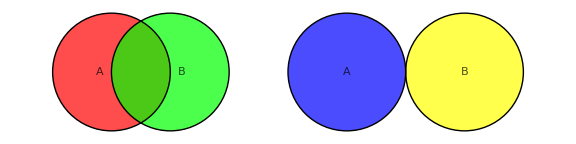

```mathematica
Show[Graphics[{Red,Opacity[0.7],Disk[{0,0},1],Black,Text["A",{-.2,0}],Green,Opacity[0.7],Disk[{1,0},1],Black,Text["B",{1.2,0}]}],
Graphics[Circle[{0,0},1]],Graphics[Circle[{1,0},1]],
Graphics[{Blue,Opacity[0.7],Disk[{4,0},1],Black,Text["A",{4,0}],Yellow,Opacity[0.7],Disk[{6,0},1],Black,Text["B",{6,0}]}],
Graphics[Circle[{4,0},1]],Graphics[Circle[{6,0},1]]]
```

Two events are mutually exclusive or disjoint if they cannot occur at the same time.

### The Addition Rule for Disjoint Events

If A and B are disjoint events, then

P(A or B) = P(A)+P(B)

### Example

Recall the blood type example:

```mathematica
PieChart[{.44,.42,.1,.04},ChartLabels->{"O 44%","A 42%", "B 10%", "AB 4%"},ChartElementFunction->"GlassSector",ChartStyle->{Red},PlotLabel->"Blood Types", ImageSize->240]
```

-Graphics-

Here is some additional information:

A person with type A can donate blood to a person with type A or AB.

A person with type B can donate blood to a person with type B or AB.

A person with type AB can donate blood to a person with type AB.

A person with type O blood can donate to anyone.

What is the probability that a randomly chosen person is a potential donor for a person with blood type A?

## Rounding Rule of Thumb for Probability

Follow the following general guidelines in this course. If in doubt carry more decimal places. If we specify give exactly what is requested.

In general you should carry probabilities to at least 4 decimal places for intermediate steps.

We often round our final answer to two or three decimal places.

For extremely small probabilities, it is important to have one or two significant digits, such as 0.000001 or 0.000034, etc.

## Exercises

Consider the following table regarding the periodontal status of individuals and their gender in a clinic. Periodontal status refers to gum disease where individuals are classified as either healthy, have gingivitis, or have periodontal disease.

What is the probability that a patient is female in this clinic?

What is the probability that a patient is female and is healthy?

What is the probability that a patient is not healthy?

What is the probability that a patient is male or has gingivitis?

Given that a patient is male, what is the probability that he is healthy?

## Further Explorations

We can extend our probability rule to three or more events. The following Venn Diagram shows all 127 nonempty unions and intersections of three events A, B, and C.

Reference

G. Beck and L. Kent, “Venn Diagrams”, http://demonstrations.wolfram.com/VennDiagrams/

Authorship information

Jie Frye

June 28, 2017

jiefrye@gmail.com